```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/00_SplinePack-034.nb"]//Quiet;

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"]//Quiet;

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"]//Quiet;
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

FileDate::zfname: The file name cannot be an empty string.

Part::partd: Part specification Null⟦3⟧ is longer than depth of object.

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FileByteCount::zfname: The file name cannot be an empty string.

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Clear::wrsym: Symbol Discard is Protected.

SetDelayed::write: Tag Discard in Discard[M_,S_] is Protected.

```mathematica
Clear[e,f,F,G,h,M,n,P,p,Q,q,R,s,μ,σ]
```

```mathematica
{M,G,h} = Get[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20241123-01/Fig/TaskPlots/P-s/Breathing.dat"];
```

```mathematica
n =   Length[M]
μ = First/@M
σ =   Last/@M
OrderedQ[μ]
```

35

{-199.,-187.,-157.,-150.,-145.,-127.,-105.,-98.,-48.,-44.,-11.,-2.,-1.,21.,21.,23.,39.,48.,48.,86.,93.,117.,119.,149.,181.,181.,200.,204.,228.,274.,296.,350.,455.,559.,589.}

{335.,432.,302.,196.,266.,237.,151.,171.,198.,210.,196.,317.,79.,124.,244.,166.,213.,35.,164.,191.,95.,304.,151.,368.,209.,223.,83.,140.,153.,317.,224.,175.,302.,443.,354.}

True

```mathematica
μ = (μ-33.44305555555555)/1.0203022278060616
σ =                                                   σ/1.0203022278060616
```

{-227.818,-216.057,-186.654,-179.793,-174.892,-157.251,-135.688,-128.828,-79.8225,-75.9021,-43.5587,-34.7378,-33.7577,-12.1955,-12.1955,-10.2353,5.44637,14.2673,14.2673,51.5112,58.3719,81.8943,83.8545,113.258,144.621,144.621,163.243,167.163,190.686,235.77,257.333,310.258,413.169,515.099,544.502}

{328.334,423.404,295.991,192.1,260.707,232.284,147.995,167.597,194.06,205.821,192.1,310.692,77.428,121.533,239.145,162.697,208.762,34.3036,160.737,187.199,93.1097,297.951,147.995,360.677,204.841,218.563,81.3484,137.214,149.956,310.692,219.543,171.518,295.991,434.185,346.956}

```mathematica
Q = LogNormalDistribution[e,s];
startpar = FindDistributionParameters[Select[μ,Positive],Q];
p = N[Range[n]/(1+n)];
q = Quantile[Q,p];
f = μ-q;
f /= σ;
f = f.f;
f = FindMinimum[f,List@@@startpar];
Q = Q/.Last[f];
```

Measurement | TaskPlots
P-s
Breathing
n | 35
p-value (χ^2) | 2.36902×10^-6
Distribution | LogNormalDistribution[3.61483,1.59448]
Mode | 2.92256
Median | 37.145
Mean | 132.425
Quartiles | 12.6717
37.145
108.885
StandardDeviation | 453.151

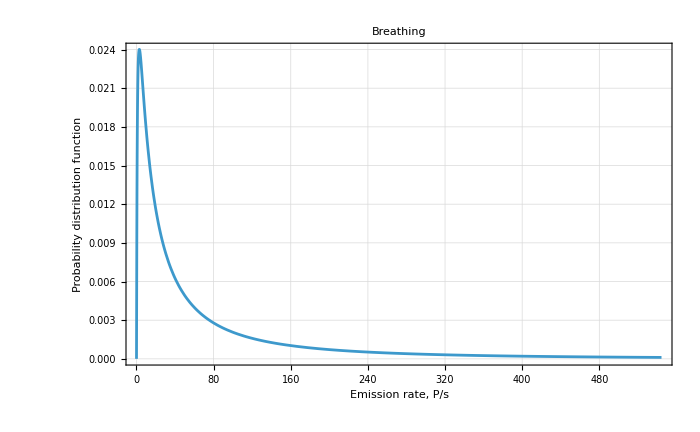

```mathematica
P = {Median,Mean,Quartiles,StandardDeviation};
P = Rule@@@Transpose[{ToString/@P,Map[#[Q]&,P]}];
PrependTo[P,"Mode"->("Median"^3/"Mean"^2)/.P];                                      (*    gilt nur für die LogNormalVerteilung    *)
PrependTo[P,"Distribution"->Q];
PrependTo[P,"p-value (χ^2)"->CDF[ChiSquareDistribution[n-2],First[f]]];
PrependTo[P,"n"->n];
PrependTo[P,"Measurement"->(taskname=Take[StringSplit[F,{".","/"}],{-4,-2}])];
TableForm[List@@@P]

Plot[
PDF[Q,x],{x,0,Last[μ]},
Frame->True,
FrameLabel->{Last[FrameLabel/.Rest[List@@G]],"Probability distribution function"},
GridLines->Automatic,
ImageSize->700,
LabelStyle->{
FontColor->GrayLevel[0],
FontFamily->"Lucida Sans Unicode",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->14},
PlotLabel->Last["Measurement"/.P],
PlotRange->All]
```

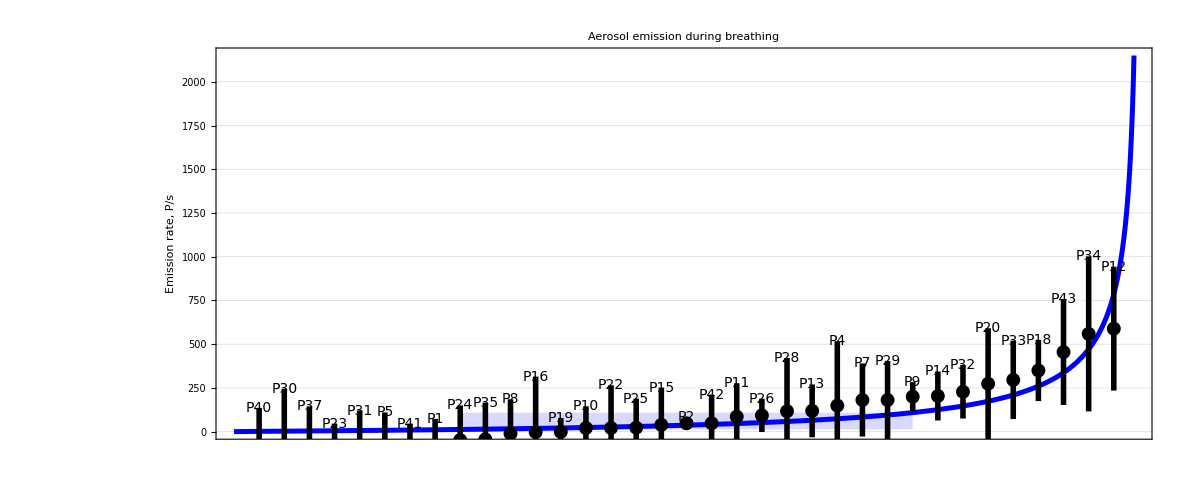

```mathematica
Clear[f];
f[k_] := Quantile[Q,k/(1+n)];
L = Plot[f[x],{x,0,n+1},DisplayFunction->Identity,PlotRange->(PlotRange/.Rest[List@@G])];
L = Extract[L,Most[First[Position[L,Line]]]];
R = Transpose[{(1+n)*{1,3}/4.,("Quartiles"/.P)[[{1,3}]]}];
h = ReplacePart[G,
Prepend[G[[1]],
{Blue,
{Opacity[0.15],Rectangle@@R},
{Thickness[0.003],L}}
],1];
h = h/.{
"Arial"->"Lucida Sans Unicode",
(FontSize -> 16)->(FontSize -> 14)}
```

```mathematica
Export[StringJoin[NotebookDirectory[],"\\output directory\\",
"Breathing","_noWLC_lognormal.svg"],h]
```

C:\Users\mona_\Downloads\upload aerosol study 2020\\output directory\Breathing_noWLC_lognormal.svg

```mathematica
(*

ENDE

*)
```

```mathematica
Clear[L,k,n]
```

```mathematica
L = p^k*(1-p)^(1+n-k)
```

(1-p)^(1-k+n) p^k

```mathematica
Solve[D[Log[L],p]/L==0,p]
```

{{p→ConditionalExpression[0, Re[k]<-1]},{p→ConditionalExpression[1, Re[n]<-2+Re[k]]},{p→k/(1+n)}}